# Método de los momentos - Chi cuadrado

```mathematica
SeedRandom[1234]
```

```mathematica
datos2=RandomVariate[ChiSquareDistribution[5],10^4]
```

{4.76251,1.52784,4.3168,3.1357,7.60988,6.72557,3.10146,8.16771,3.51012,8.22688,5.71352,1.25888,10.5185,11.4054,5.21046,9970,5.26502,0.942671,3.85939,2.33098,4.34013,2.06446,0.504719,1.06145,2.68873,2.77825,2.44833,10.6619,9.3595,1.46811,2.68483}
 |  |  |  |

```mathematica
RandomVariate[ChiSquareDistribution[5],3]
```

{9.17045,3.00851,4.61681}

```mathematica
datos=ReplacePart[datos2,{2514-> 9.170447257086153,4287-> 3.008506020714771,8676-> 4.6168058605179905}]
```

{4.76251,1.52784,4.3168,3.1357,7.60988,6.72557,3.10146,8.16771,3.51012,8.22688,5.71352,1.25888,10.5185,11.4054,5.21046,9970,5.26502,0.942671,3.85939,2.33098,4.34013,2.06446,0.504719,1.06145,2.68873,2.77825,2.44833,10.6619,9.3595,1.46811,2.68483}
 |  |  |  |

```mathematica
Length[datos]
```

10000

### MOP DE GRADO 3

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M3 = {{15625/3,390625/4,1953125 },{390625/4,1953125 ,244140625/6},{1953125 ,244140625/6,6103515625/7}}
```

{{15625/3,390625/4,1953125},{390625/4,1953125,244140625/6},{1953125,244140625/6,6103515625/7}}

```mathematica
MatrixForm[M3]
```

(15625/3 | 390625/4 | 1953125
390625/4 | 1953125 | 244140625/6
1953125 | 244140625/6 | 6103515625/7)

```mathematica
B3 = {(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4)}
```

{5.06637,35.7888,322.891}

```mathematica
Sol3 = Inverse[M3].B3
```

{0.0356472,-0.00389574,0.000102322}

```mathematica
(*Obtención de la densidad y representación*)
```

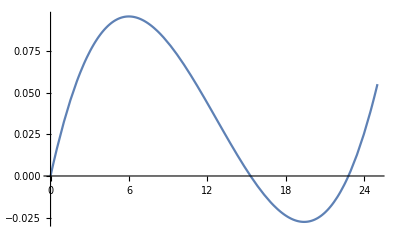

```mathematica
Plot[b*x+c*x^2+d*x^3/.{b->0.035647208463115074,c->-0.0038957430998472096,d->0.00010232191489544248},{x,0,25}]
```

```mathematica
F3[x_]=b*x+c*x^2+d*x^3/.{b->0.035647208463115074,c->-0.0038957430998472096,d->0.00010232191489544248}
```

0.0356472 x-0.00389574 x^2+0.000102322 x^3

```mathematica
FindMinimum[F3[x],{x,15}]
```

{-0.0275545,{x→19.3947}}

```mathematica
Integrate[F3[x]+0.02755449539853916,{x,0,25}]
```

1.53066

```mathematica
f3[x_]=(b*x+c*x^2+d*x^3+0.02755449539853916)/1.5306608861574453/.{b->0.035647208463115074,c->-0.0038957430998472096,d->0.00010232191489544248}
```

0.653313 (0.0275545+0.0356472 x-0.00389574 x^2+0.000102322 x^3)

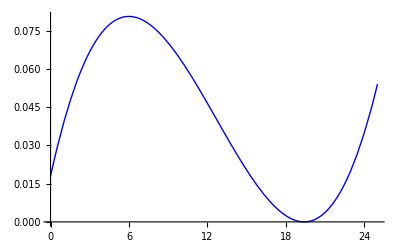

```mathematica
Plot[f3[x],{x,0,25},PlotStyle->{Blue,Thin}]
```

```mathematica
Solve[f3[x]==0,Reals]
```

{{x→-0.715912},{x→19.3947},{x→19.3947}}

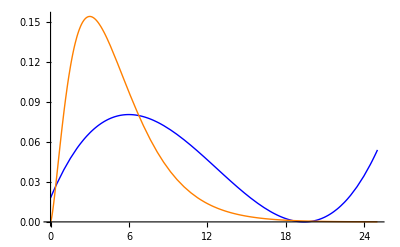

```mathematica
Plot[{f3[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]=(PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KL3=N[Integrate[G[x]*Log[G[x]/f3[x]],{x,0,25}]]
```

0.333387

```mathematica
(*Verosimilitud*)
```

```mathematica
f3[datos]
```

{0.0784081,0.0478806,0.076484,0.068064,0.0772961,0.0798435,0.0677433,0.0748519,0.0712806,0.0745583,0.0804464,0.0434193,0.0591683,0.0517192,9972,0.0377497,0.0738154,0.0593051,0.076601,0.0558213,0.0291162,0.0399339,0.0635188,0.0644922,0.060745,0.0580032,0.0678267,0.0469181,0.0634756}
 |  |  |  |

```mathematica
x3=Log[f3[datos]]
```

{-2.54583,-3.03905,-2.57067,-2.68731,-2.56011,-2.52769,-2.69203,-2.59224,-2.64113,-2.59617,-2.52016,-3.13685,-2.82737,-2.96193,9972,-3.27678,-2.60619,-2.82506,-2.56915,-2.8856,-3.53646,-3.22053,-2.75642,-2.74121,-2.80107,-2.84726,-2.6908,-3.05935,-2.7571}
 |  |  |  |

```mathematica
V3 =Apply[Plus,x3]
```

-27549.5

### MOP DE GRADO 4

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6

```mathematica
Integrate[x^2(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7

```mathematica
Integrate[x^3(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8

```mathematica
Integrate[x^4(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M4 = {{15625/3,390625/4,1953125 ,244140625/6},{390625/4,1953125 ,244140625/6,6103515625/7},{1953125 ,244140625/6,6103515625/7,152587890625/8},{244140625/6,6103515625/7,152587890625/8,3814697265625/9}}
```

{{15625/3,390625/4,1953125,244140625/6},{390625/4,1953125,244140625/6,6103515625/7},{1953125,244140625/6,6103515625/7,152587890625/8},{244140625/6,6103515625/7,152587890625/8,3814697265625/9}}

```mathematica
MatrixForm[M4]
```

(15625/3 | 390625/4 | 1953125 | 244140625/6
390625/4 | 1953125 | 244140625/6 | 6103515625/7
1953125 | 244140625/6 | 6103515625/7 | 152587890625/8
244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9)

```mathematica
B4={(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88}

```mathematica
Sol4=Inverse[M4].B4
```

{0.0724753,-0.0127345,0.000721035,-0.0000131992}

```mathematica
(*Obtención de la densidad y representación*)
```

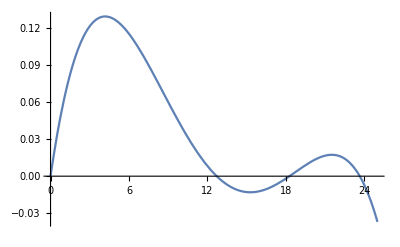

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4/.{b->0.07247534552936244,c->-0.012734495995746598,d->0.0007210346176084008,e->-0.000013199204324543091},{x,0,25}]
```

```mathematica
F4[x_]=b*x+c*x^2+d*x^3+e*x^4/.{b->0.07247534552936244,c->-0.012734495995746598,d->0.0007210346176084008,e->-0.000013199204324543091}
```

0.0724753 x-0.0127345 x^2+0.000721035 x^3-0.0000131992 x^4

```mathematica
F4[25]
```

-0.0369496

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+0.036949648250945266/.{b->0.07247534552936244,c->-0.012734495995746598,d->0.0007210346176084008,e->-0.000013199204324543091},{x,0,25}]
```

1.88063

```mathematica
f4[x_]=(b*x+c*x^2+d*x^3+e*x^4+0.036949648250945266)/1.8806276357996943/.{b->0.07247534552936244,c->-0.012734495995746598,d->0.0007210346176084008,e->-0.000013199204324543091}
```

0.531737 (0.0369496+0.0724753 x-0.0127345 x^2+0.000721035 x^3-0.0000131992 x^4)

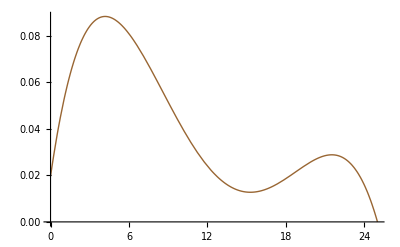

```mathematica
Plot[f4[x],{x,0,25},PlotStyle->{Brown,Thin}]
```

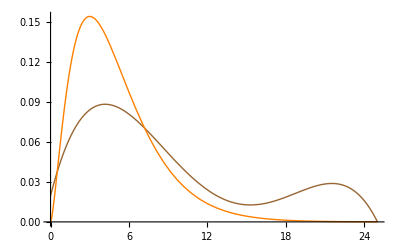

```mathematica
Plot[{f4[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Brown,Thin},{Orange,Thin}}]
```

```mathematica
Solve[f4[x]==0,Reals]
```

{{x→-0.469973},{x→25.}}

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL4=N[Integrate[G[x]*Log[G[x]/f4[x]],{x,0,25}]]
```

0.263958

```mathematica
(*Verosimilitud*)
```

```mathematica
f4[datos]
```

{0.0874034,0.0640499,0.0882287,0.0850525,0.0662056,0.0748213,0.0848252,0.0603551,0.0870057,0.0597248,0.0828167,0.0581781,0.0360985,0.0284096,9972,0.0502744,0.0880035,0.077335,0.0882098,0.0735936,0.0374222,0.0533739,0.0813986,0.0822527,0.0787855,0.0347755,0.0476553,0.0628112,0.0813599}
 |  |  |  |

```mathematica
x4=Log[f4[datos]]
```

{-2.43722,-2.74809,-2.42782,-2.46449,-2.71499,-2.59265,-2.46716,-2.80751,-2.44178,-2.81801,-2.49113,-2.84425,-3.3215,-3.56103,9972,-2.99026,-2.43038,-2.55961,-2.42804,-2.6092,-3.28549,-2.93043,-2.5084,-2.49796,-2.54103,-3.35884,-3.04376,-2.76762,-2.50887}
 |  |  |  |

```mathematica
V4=Apply[Plus,x4]
```

-26891.4

### MOP DE GRADO 5

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7==(Apply[Plus,datos])/(10^4),(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8==(Apply[Plus,datos^2])/(10^4),1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9==(Apply[Plus,datos^3])/(10^4),(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2==(Apply[Plus,datos^4])/(10^4),(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11==(Apply[Plus,datos^5])/(10^4)},{b,c,d,e,f}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{8.71931×10^8,4.06901×10^7,1.95313×10^6,97656.3,5208.33,-5.06637},{1.90735×10^10,8.71931×10^8,4.06901×10^7,1.95313×10^6,97656.3,-35.7888},{4.23855×10^11,1.90735×10^10,8.71931×10^8,«22»,1.95313×10^6,-322.891},{9.53674×10^12,4.23855×10^11,1.90735×10^10,8.71931×10^8,4.06901×10^7,-3521.88},{2.16744×10^14,9.53674×10^12,4.23855×10^11,1.90735×10^10,8.71931×10^8,-44666.}} may contain significant numerical errors.

{{b→0.103854,c→-0.0244492,d→0.0021268,e→-0.0000806761,f→1.12461×10^-6}}

```mathematica
(*Obtención de la densidad y representación*)
```

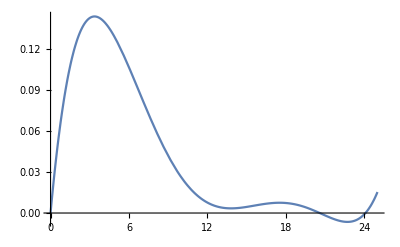

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->0.10385410186213821,c->-0.024449231693309228,d->0.0021268029013151997,e->-0.00008067608194244087,f->1.124614626964562*^-6},{x,0,25}]
```

```mathematica
F5[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->0.10385410186213821,c->-0.024449231693309228,d->0.0021268029013151997,e->-0.00008067608194244087,f->1.124614626964562*^-6}
```

0.103854 x-0.0244492 x^2+0.0021268 x^3-0.0000806761 x^4+1.12461×10^-6 x^5

```mathematica
FindMinimum[F5[x],{x,22}]
```

{-0.00649419,{x→22.704}}

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+0.006494185823917142/.{b->0.10385410186213821,c->-0.024449231693309228,d->0.0021268029013151997,e->-0.00008067608194244087,f->1.124614626964562*^-6},{x,0,25}]
```

1.16282

```mathematica
f5[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+0.006494185823917142)/1.1628226811415345/.{b->0.10385410186213821,c->-0.024449231693309228,d->0.0021268029013151997,e->-0.00008067608194244087,f->1.124614626964562*^-6}
```

0.859976 (0.00649419+0.103854 x-0.0244492 x^2+0.0021268 x^3-0.0000806761 x^4+1.12461×10^-6 x^5)

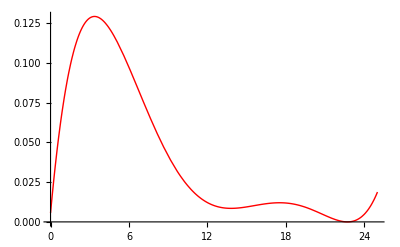

```mathematica
Plot[f5[x],{x,0,25},PlotStyle->{Red,Thin}]
```

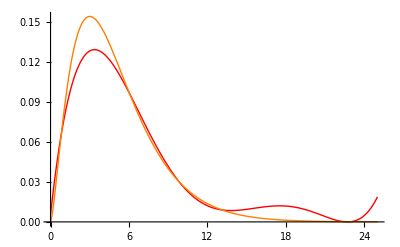

```mathematica
Plot[{f5[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL5=N[Integrate[G[x]*Log[G[x]/f5[x]],{x,0,25}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {22.7047}. NIntegrate obtained 0.0577831 and 8.2946×10^-7 for the integral and error estimates.

0.0577831

```mathematica
(*Verosimilitud*)
```

```mathematica
x5=Log[f5[datos]]
```

{-2.13465,-2.3115,-2.08906,-2.04887,-2.72319,-2.48931,-2.04982,-2.89366,-2.04711,-2.91278,-2.27704,-2.42844,-3.79381,-4.17557,9972,-2.62319,-2.05827,-2.11437,-2.09108,-2.16088,-3.08923,-2.54089,-2.07321,-2.06614,-2.09842,-3.85575,-3.31636,-2.3345,-2.07355}
 |  |  |  |

```mathematica
V5=Apply[Plus,x5]
```

-24887.5

### MOP DE GRADO 6

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M6={{15625/3,390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8},{390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9},{1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13}}
```

{{15625/3,390625/4,1953125,244140625/6,6103515625/7,152587890625/8},{390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9},{1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13}}

```mathematica
MatrixForm[M6]
```

(15625/3 | 390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8
390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9
1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2
244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11
6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12
152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13)

```mathematica
B6 = {(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.}

```mathematica
Sol6 = Inverse[M6].B6
```

{0.118037,-0.0320137,0.00348841,-0.000189605,5.11866×10^-6,-5.47755×10^-8}

```mathematica
(*Obtención de la densidad y representación*)
```

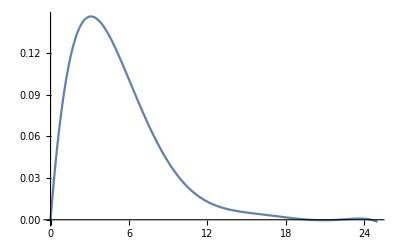

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->0.11803749424464804,c->-0.032013707630941635,d->0.003488408570129206,e->-0.00018960453545012555,f->5.118657922321306*^-6,g->-5.477545090860714*^-8},{x,0,25}]
```

```mathematica
F6[x_]= b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->0.11803749424464804,c->-0.032013707630941635,d->0.003488408570129206,e->-0.00018960453545012555,f->5.118657922321306*^-6,g->-5.477545090860714*^-8}
```

0.118037 x-0.0320137 x^2+0.00348841 x^3-0.000189605 x^4+5.11866×10^-6 x^5-5.47755×10^-8 x^6

```mathematica
FindMinimum[F6[x],{x,23}]
```

{-0.00035195,{x→20.8817}}

```mathematica
F6[25]
```

-0.00153671

```mathematica
Integrate[  b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+0.0015367119739266855/.{b->0.11803749424464804,c->-0.032013707630941635,d->0.003488408570129206,e->-0.00018960453545012555,f->5.118657922321306*^-6,g->-5.477545090860714*^-8},{x,0,25}]
```

1.04894

```mathematica
f6[x_]= (b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+0.0015367119739266855)/1.0489364246918456/.{b->0.11803749424464804,c->-0.032013707630941635,d->0.003488408570129206,e->-0.00018960453545012555,f->5.118657922321306*^-6,g->-5.477545090860714*^-8}
```

0.953347 (0.00153671+0.118037 x-0.0320137 x^2+0.00348841 x^3-0.000189605 x^4+5.11866×10^-6 x^5-5.47755×10^-8 x^6)

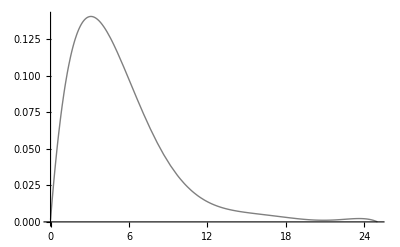

```mathematica
Plot[f6[x],{x,0,25},PlotStyle->{Gray,Thin}]
```

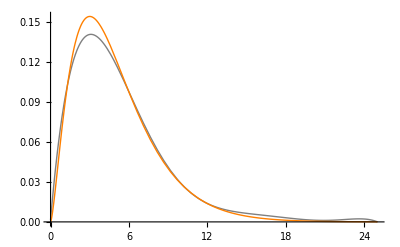

```mathematica
Plot[{f6[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Gray,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL6=N[Integrate[G[x]*Log[G[x]/f6[x]],{x,0,25}]]
```

0.0118943

```mathematica
(*Verosimilitud*)
```

```mathematica
x6=Log[f6[datos]]
```

{-2.09763,-2.17978,-2.03842,-1.96094,-2.74625,-2.5013,-1.96082,-2.91786,-1.97102,-2.93678,-2.26671,-2.29307,-3.74701,-4.07427,9972,-2.48807,-1.99327,-2.00209,-2.04117,-2.0413,-2.97784,-2.40486,-1.97146,-1.96712,-1.98953,-3.80041,-3.32177,-2.20177,-1.97168}
 |  |  |  |

```mathematica
V6=Apply[Plus,x6]
```

-24436.8

### MOP DE GRADO 7

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M7={{15625/3,390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9},{390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3}}
```

{{15625/3,390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9},{390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3}}

```mathematica
MatrixRank[M7]
```

7

```mathematica
B7={(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7}

```mathematica
Sol7=Inverse[M7].B7
```

{0.115727,-0.0303499,0.00307247,-0.000140801,2.19042×10^-6,3.22349×10^-8,-1.01512×10^-9}

```mathematica
(*Obtención de la densidad y representación*)
```

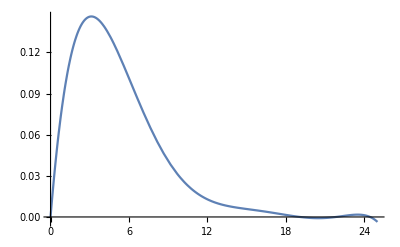

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.11572670412307096,c->-0.030349938743408078,d->0.0030724663482449843,e->-0.0001408006480826396,f->2.1904246802701213*^-6,g->3.22349082838673*^-8,h->-1.015120857244854*^-9},{x,0,25}]
```

```mathematica
F7[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.11572670412307096,c->-0.030349938743408078,d->0.0030724663482449843,e->-0.0001408006480826396,f->2.1904246802701213*^-6,g->3.22349082838673*^-8,h->-1.015120857244854*^-9}
```

0.115727 x-0.0303499 x^2+0.00307247 x^3-0.000140801 x^4+2.19042×10^-6 x^5+3.22349×10^-8 x^6-1.01512×10^-9 x^7

```mathematica
FindMinimum[F7[x],{x,23}]
```

{-0.000885303,{x→20.4728}}

```mathematica
F7[25]
```

-0.00359992

```mathematica
Integrate[F7[x]+0.0035999174599048445,{x,0,25}]
```

1.0996

```mathematica
f7[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+0.0035999174599048445)/1.0995954878122802/.{b->0.11572670412307096,c->-0.030349938743408078,d->0.0030724663482449843,e->-0.0001408006480826396,f->2.1904246802701213*^-6,g->3.22349082838673*^-8,h->-1.015120857244854*^-9}
```

0.909425 (0.00359992+0.115727 x-0.0303499 x^2+0.00307247 x^3-0.000140801 x^4+2.19042×10^-6 x^5+3.22349×10^-8 x^6-1.01512×10^-9 x^7)

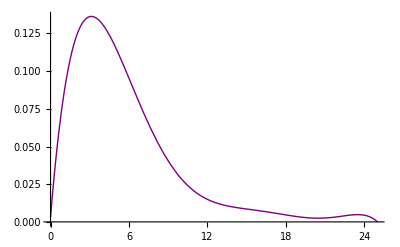

```mathematica
Plot[f7[x],{x,0,25},PlotStyle->{Purple,Thin}]
```

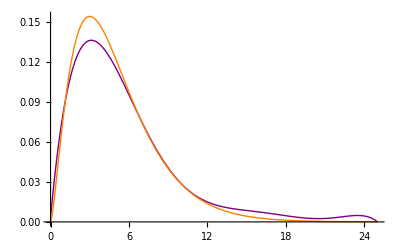

```mathematica
Plot[{f7[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Purple,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL7=N[Integrate[G[x]*Log[G[x]/f7[x]],{x,0,25}]]
```

0.0278809

```mathematica
(*Verosimilitud*)
```

```mathematica
x7=Log[f7[datos]]
```

{-2.12362,-2.21708,-2.06584,-1.9929,-2.76612,-2.52294,-1.99292,-2.93596,-2.00145,-2.95464,-2.29026,-2.33014,-3.73393,-4.02709,9972,-2.52324,-2.02233,-2.03731,-2.0685,-2.07746,-3.00149,-2.44104,-2.00527,-2.00056,-2.0243,-3.78298,-3.33125,-2.23909,-2.00551}
 |  |  |  |

```mathematica
V7=Apply[Plus,x7]
```

-24591.3

### MOP DE GRADO 8

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16

```mathematica
Integrate[x^8*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17

```mathematica
M8={{15625/3,390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17}}
```

{{15625/3,390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2},{390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17}}

```mathematica
MatrixForm[M8]
```

(15625/3 | 390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2
390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11
1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12
244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13
6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14
152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3
3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16
19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17)

```mathematica
MatrixRank[M8]
```

8

```mathematica
B8={(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4),(Apply[Plus,datos^8])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7,1.70982×10^8}

```mathematica
Sol8 = Inverse[M8].B8
```

{0.103495,-0.0189333,-0.000695027,0.000461998,-0.0000500522,2.53988×10^-6,-6.37062×10^-8,6.36862×10^-10}

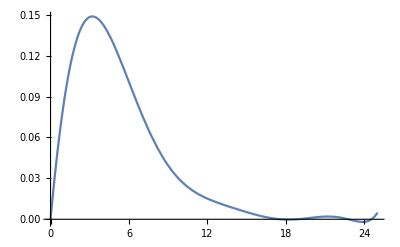

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.10349458266356493,c->-0.018933292047835337,d->-0.00069502706131086,e->0.00046199829744586474,f->-0.00005005215059859791,g->2.539878521671396*^-6,h->-6.370621119222957*^-8,i->6.368618700711115*^-10},{x,0,25}]
```

```mathematica
F8[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.10349458266356493,c->-0.018933292047835337,d->-0.00069502706131086,e->0.00046199829744586474,f->-0.00005005215059859791,g->2.539878521671396*^-6,h->-6.370621119222957*^-8,i->6.368618700711115*^-10}
```

0.103495 x-0.0189333 x^2-0.000695027 x^3+0.000461998 x^4-0.0000500522 x^5+2.53988×10^-6 x^6-6.37062×10^-8 x^7+6.36862×10^-10 x^8

```mathematica
FindMinimum[F8[x],{x,23}]
```

{-0.00192836,{x→23.8669}}

```mathematica
Integrate[F8[x]+0.0019283574747959165,{x,0,25}]
```

1.05486

```mathematica
f8[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+0.0019283574747959165)/1.0548570001769235/.{b->0.10349458266356493,c->-0.018933292047835337,d->-0.00069502706131086,e->0.00046199829744586474,f->-0.00005005215059859791,g->2.539878521671396*^-6,h->-6.370621119222957*^-8,i->6.368618700711115*^-10}
```

0.947996 (0.00192836+0.103495 x-0.0189333 x^2-0.000695027 x^3+0.000461998 x^4-0.0000500522 x^5+2.53988×10^-6 x^6-6.37062×10^-8 x^7+6.36862×10^-10 x^8)

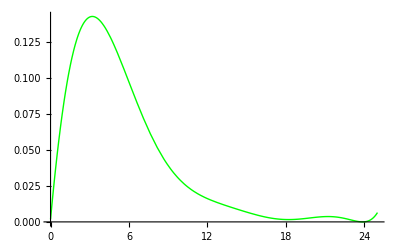

```mathematica
Plot[f8[x],{x,0,25},PlotStyle->{Green,Thin}]
```

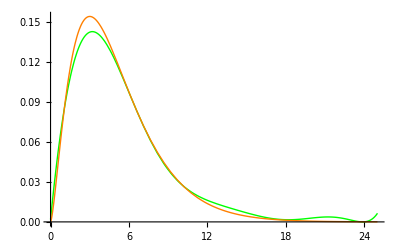

```mathematica
Plot[{f8[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Green,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL8=N[Integrate[G[x]*Log[G[x]/f8[x]],{x,0,25}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {23.849780823613858871112824999727308750152587890625}. NIntegrate obtained 0.014266 and 4.39901×10^-7 for the integral and error estimates.

0.014266

```mathematica
(*Verosimilitud*)
```

```mathematica
x8=Log[f8[datos]]
```

{-2.08126,-2.21181,-2.0188,-1.94662,-2.7858,-2.5218,-1.94699,-2.96522,-1.95264,-2.98464,-2.2648,-2.3378,-3.72551,-3.9734,9972,-2.54943,-1.97315,-2.0048,-2.02165,-2.05232,-3.06364,-2.45977,-1.96515,-1.95891,-1.98901,-3.7676,-3.36047,-2.2365,-1.96545}
 |  |  |  |

```mathematica
V8=Apply[Plus,x8]
```

-24456.5

### MOP DE GRADO 9

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2+(2384185791015625 j)/11

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11+(59604644775390625 j)/12

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12+(1490116119384765625 j)/13

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13+(37252902984619140625 j)/14

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14+(186264514923095703125 j)/3

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3+(23283064365386962890625 j)/16

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16+(582076609134674072265625 j)/17

```mathematica
Integrate[x^8*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17+(14551915228366851806640625 j)/18

```mathematica
Integrate[x^9*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,0,25}]
```

(2384185791015625 b)/11+(59604644775390625 c)/12+(1490116119384765625 d)/13+(37252902984619140625 e)/14+(186264514923095703125 f)/3+(23283064365386962890625 g)/16+(582076609134674072265625 h)/17+(14551915228366851806640625 i)/18+(363797880709171295166015625 j)/19

```mathematica
M9={{15625/3,390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18},{2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19}}
```

{{15625/3,390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11},{390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18},{2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19}}

```mathematica
MatrixForm[M9]
```

(15625/3 | 390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11
390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12
1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13
244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14
6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3
152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16
3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17
19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18
2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18 | 363797880709171295166015625/19)

```mathematica
B9= {(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4),(Apply[Plus,datos^8])/(10^4),(Apply[Plus,datos^9])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7,1.70982×10^8,3.08638×10^9}

```mathematica
Sol9=Inverse[M9].B9
```

{0.0876591,-0.000353011,-0.00849875,0.00208517,-0.000239422,0.0000155253,-5.83122×10^-7,1.18496×10^-8,-1.00915×10^-10}

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

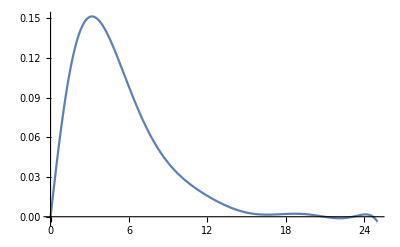

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{b->0.087659115441447,c->-0.00035301050748870466,d->-0.00849874530828032,e->0.002085171692791654,f->-0.00023942238005525418,g->0.00001552526568449064,h->-5.831216977022265*^-7,i->1.1849640626853623*^-8,j->-1.009150088097694*^-10},{x,0,25}]
```

```mathematica
F9[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{b->0.087659115441447,c->-0.00035301050748870466,d->-0.00849874530828032,e->0.002085171692791654,f->-0.00023942238005525418,g->0.00001552526568449064,h->-5.831216977022265*^-7,i->1.1849640626853623*^-8,j->-1.009150088097694*^-10}
```

0.0876591 x-0.000353011 x^2-0.00849875 x^3+0.00208517 x^4-0.000239422 x^5+0.0000155253 x^6-5.83122×10^-7 x^7+1.18496×10^-8 x^8-1.00915×10^-10 x^9

```mathematica
FindMinimum[F9[x],{x,23}]
```

{-0.00114605,{x→22.1113}}

```mathematica
F9[25]
```

-0.0039028

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+0.0039028040973789757/.{b->0.087659115441447,c->-0.00035301050748870466,d->-0.00849874530828032,e->0.002085171692791654,f->-0.00023942238005525418,g->0.00001552526568449064,h->-5.831216977022265*^-7,i->1.1849640626853623*^-8,j->-1.009150088097694*^-10},{x,0,25}]
```

1.10177

```mathematica
f9[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+0.0039028040973789757)/1.1017746181264556/.{b->0.087659115441447,c->-0.00035301050748870466,d->-0.00849874530828032,e->0.002085171692791654,f->-0.00023942238005525418,g->0.00001552526568449064,h->-5.831216977022265*^-7,i->1.1849640626853623*^-8,j->-1.009150088097694*^-10}
```

0.907627 (0.0039028+0.0876591 x-0.000353011 x^2-0.00849875 x^3+0.00208517 x^4-0.000239422 x^5+0.0000155253 x^6-5.83122×10^-7 x^7+1.18496×10^-8 x^8-1.00915×10^-10 x^9)

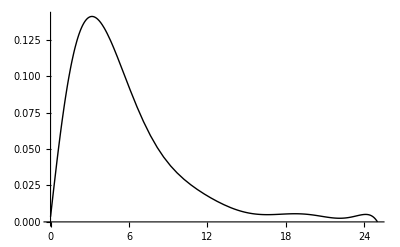

```mathematica
Plot[f9[x],{x,0,25},PlotStyle->{Black,Thin}]
```

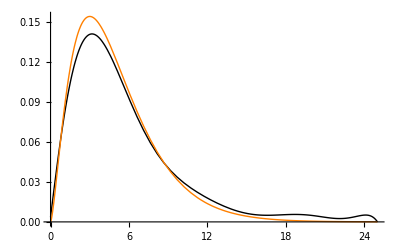

```mathematica
Plot[{f9[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Black,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL9=N[Integrate[G[x]*Log[G[x]/f9[x]],{x,0,25}]]
```

0.0285553

```mathematica
(*Verosimilitud*)
```

```mathematica
x9=Log[f9[datos]]
```

{-2.11277,-2.24891,-2.04319,-1.95861,-2.81743,-2.5694,-1.95888,-2.97621,-1.96687,-2.99298,-2.30979,-2.3868,-3.61468,-3.85507,9972,-2.6154,-1.99109,-2.02078,-2.0464,-2.07309,-3.15259,-2.51905,-1.97761,-1.97096,-2.00349,-3.65277,-3.30668,-2.27602,-1.97794}
 |  |  |  |

```mathematica
V9=Apply[Plus,x9]
```

-24593.1

### MOP DE GRADO 10

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2+(2384185791015625 j)/11+(59604644775390625 k)/12

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11+(59604644775390625 j)/12+(1490116119384765625 k)/13

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12+(1490116119384765625 j)/13+(37252902984619140625 k)/14

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13+(37252902984619140625 j)/14+(186264514923095703125 k)/3

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14+(186264514923095703125 j)/3+(23283064365386962890625 k)/16

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3+(23283064365386962890625 j)/16+(582076609134674072265625 k)/17

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16+(582076609134674072265625 j)/17+(14551915228366851806640625 k)/18

```mathematica
Integrate[x^8*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17+(14551915228366851806640625 j)/18+(363797880709171295166015625 k)/19

```mathematica
Integrate[x^9*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(2384185791015625 b)/11+(59604644775390625 c)/12+(1490116119384765625 d)/13+(37252902984619140625 e)/14+(186264514923095703125 f)/3+(23283064365386962890625 g)/16+(582076609134674072265625 h)/17+(14551915228366851806640625 i)/18+(363797880709171295166015625 j)/19+(1818989403545856475830078125 k)/4

```mathematica
Integrate[x^10*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10),{x,0,25}]
```

(59604644775390625 b)/12+(1490116119384765625 c)/13+(37252902984619140625 d)/14+(186264514923095703125 e)/3+(23283064365386962890625 f)/16+(582076609134674072265625 g)/17+(14551915228366851806640625 h)/18+(363797880709171295166015625 i)/19+(1818989403545856475830078125 j)/4+(227373675443232059478759765625 k)/21

```mathematica
(*Soución matricial del sistema*)
```

```mathematica
M10={{15625/3,390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{390625/4,1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{1953125 ,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19},{2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19,1818989403545856475830078125/4},{59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19,1818989403545856475830078125/4,227373675443232059478759765625/21}}
```

{{15625/3,390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12},{390625/4,1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13},{1953125,244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14},{244140625/6,6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3},{6103515625/7,152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16},{152587890625/8,3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17},{3814697265625/9,19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18},{19073486328125/2,2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19},{2384185791015625/11,59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19,1818989403545856475830078125/4},{59604644775390625/12,1490116119384765625/13,37252902984619140625/14,186264514923095703125/3,23283064365386962890625/16,582076609134674072265625/17,14551915228366851806640625/18,363797880709171295166015625/19,1818989403545856475830078125/4,227373675443232059478759765625/21}}

```mathematica
MatrixRank[M10]
```

10

```mathematica
MatrixForm[M10]
```

(15625/3 | 390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12
390625/4 | 1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13
1953125 | 244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14
244140625/6 | 6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3
6103515625/7 | 152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16
152587890625/8 | 3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17
3814697265625/9 | 19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18
19073486328125/2 | 2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18 | 363797880709171295166015625/19
2384185791015625/11 | 59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18 | 363797880709171295166015625/19 | 1818989403545856475830078125/4
59604644775390625/12 | 1490116119384765625/13 | 37252902984619140625/14 | 186264514923095703125/3 | 23283064365386962890625/16 | 582076609134674072265625/17 | 14551915228366851806640625/18 | 363797880709171295166015625/19 | 1818989403545856475830078125/4 | 227373675443232059478759765625/21)

```mathematica
B10={(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4),(Apply[Plus,datos^8])/(10^4),(Apply[Plus,datos^9])/(10^4),(Apply[Plus,datos^10])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7,1.70982×10^8,3.08638×10^9,5.8461×10^10}

```mathematica
Sol10 = Inverse[M10].B10
```

{0.0729767,0.0207897,-0.0194929,0.00495832,-0.000670395,0.0000549285,-2.81597×10^-6,8.84045×10^-8,-1.55546×10^-9,1.17539×10^-11}

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

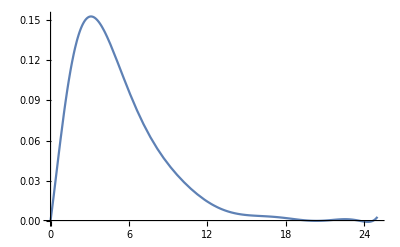

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10/.{b->0.07297668754159758,c->0.020789685667580216,d->-0.019492947320031817,e->0.004958323151875277,f->-0.0006703950988713459,g->0.000054928485697325335,h->-2.8159708314323684*^-6,i->8.84044680834594*^-8,j->-1.5554567300791935*^-9,k->1.1753872496336954*^-11},{x,0,25}]
```

```mathematica
F10[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10/.{b->0.07297668754159758,c->0.020789685667580216,d->-0.019492947320031817,e->0.004958323151875277,f->-0.0006703950988713459,g->0.000054928485697325335,h->-2.8159708314323684*^-6,i->8.84044680834594*^-8,j->-1.5554567300791935*^-9,k->1.1753872496336954*^-11}
```

0.0729767 x+0.0207897 x^2-0.0194929 x^3+0.00495832 x^4-0.000670395 x^5+0.0000549285 x^6-2.81597×10^-6 x^7+8.84045×10^-8 x^8-1.55546×10^-9 x^9+1.17539×10^-11 x^10

```mathematica
FindMinimum[F10[x],{x,24}]
```

{-0.00101079,{x→24.2557}}

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+0.0010107938409191775/.{b->0.07297668754159758,c->0.020789685667580216,d->-0.019492947320031817,e->0.004958323151875277,f->-0.0006703950988713459,g->0.000054928485697325335,h->-2.8159708314323684*^-6,i->8.84044680834594*^-8,j->-1.5554567300791935*^-9,k->1.1753872496336954*^-11},{x,0,25}]
```

1.02797

```mathematica
f10[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+0.0010107938409191775)/1.0279708888028836/.{b->0.07297668754159758,c->0.020789685667580216,d->-0.019492947320031817,e->0.004958323151875277,f->-0.0006703950988713459,g->0.000054928485697325335,h->-2.8159708314323684*^-6,i->8.84044680834594*^-8,j->-1.5554567300791935*^-9,k->1.1753872496336954*^-11}
```

0.97279 (0.00101079+0.0729767 x+0.0207897 x^2-0.0194929 x^3+0.00495832 x^4-0.000670395 x^5+0.0000549285 x^6-2.81597×10^-6 x^7+8.84045×10^-8 x^8-1.55546×10^-9 x^9+1.17539×10^-11 x^10)

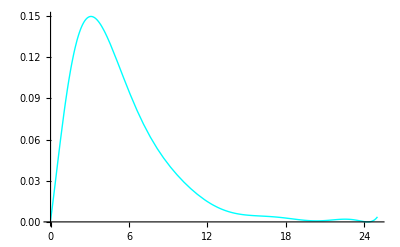

```mathematica
Plot[f10[x],{x,0,25},PlotStyle->{Cyan,Thin}]
```

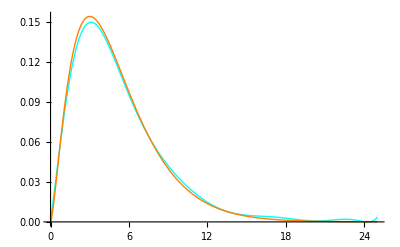

```mathematica
Plot[{f10[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Cyan,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL10=N[Integrate[G[x]*Log[G[x]/f10[x]],{x,0,25}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24.24709386033466229637411970543325878679752349853515625}. NIntegrate obtained 0.00617627 and 1.6128×10^-6 for the integral and error estimates.

0.00617627

```mathematica
(*Verosimilitud*)
```

```mathematica
x10=Log[f10[datos]]
```

{-2.07782,-2.20266,-2.00157,-1.89845,-2.77698,-2.53879,-1.89831,-2.93118,-1.91194,-2.94772,-2.28286,-2.35574,-3.64849,-3.97504,9972,-2.6125,-1.94184,-1.95672,-2.00516,-2.01159,-3.22338,-2.50395,-1.91359,-1.90743,-1.93906,-3.69862,-3.27524,-2.2326,-1.9139}
 |  |  |  |

```mathematica
V10=Apply[Plus,x10]
```

-24371.9

### GRÁFICO DIVERGENCIAS

```mathematica
DKL = {{{3,0.33338684146652753}},{{4,0.26395823590229167}},{{5,0.05778311101566449}},{{6,0.011894281506145618}},{{7,0.02788091299296159}},{{8,0.014265970360696554}},{{9,0.028555304593343926}},{{10,0.006176270197469441}}}
```

{{{3,0.333387}},{{4,0.263958}},{{5,0.0577831}},{{6,0.0118943}},{{7,0.0278809}},{{8,0.014266}},{{9,0.0285553}},{{10,0.00617627}}}

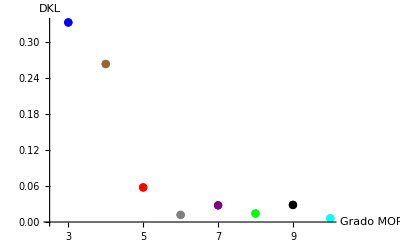

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],Ticks->{{3,4,5,6,7,8,9,10}, Automatic}]
```

```mathematica
DKL1 = {{3,0.33338684146652753},{4,0.26395823590229167},{5,0.05778311101566449},{6,0.011894281506145618},{7,0.02788091299296159},{8,0.014265970360696554},{9,0.028555304593343926},{10,0.006176270197469441}}
```

{{3,0.333387},{4,0.263958},{5,0.0577831},{6,0.0118943},{7,0.0278809},{8,0.014266},{9,0.0285553},{10,0.00617627}}

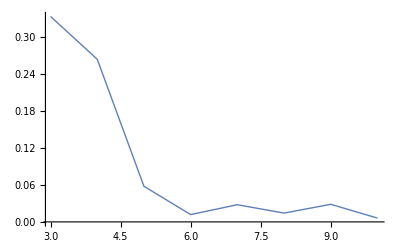

```mathematica
g2 = ListLinePlot[DKL1,PlotStyle->Thin]
```

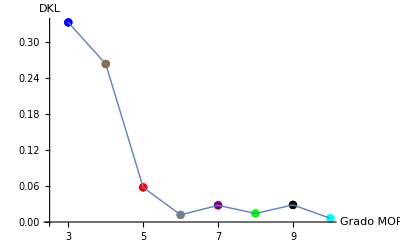

```mathematica
GrafDivMChi=Show[g1,g2]
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,-27549.470782602206}},{{4,-26891.42228530712}},{{5,-24887.54866634809}},{{6,-24436.795781728208}},{{7,-24436.795781728208}},{{8,-24456.47446809008}},{{9,-24593.098284052234}},{{10,-24371.9266976381}}}
```

{{{3,-27549.5}},{{4,-26891.4}},{{5,-24887.5}},{{6,-24436.8}},{{7,-24436.8}},{{8,-24456.5}},{{9,-24593.1}},{{10,-24371.9}}}

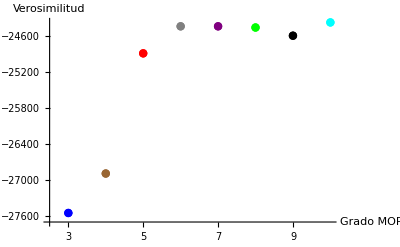

```mathematica
h1 =ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-27700},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,4,5,6,7,8,9,10}, Automatic}]
```

```mathematica
V1 = {{3,-27549.470782602206},{4,-26891.42228530712},{5,-24887.54866634809},{6,-24436.795781728208},{7,-24436.795781728208},{8,-24456.47446809008},{9,-24593.098284052234},{10,-24371.9266976381}}
```

{{3,-27549.5},{4,-26891.4},{5,-24887.5},{6,-24436.8},{7,-24436.8},{8,-24456.5},{9,-24593.1},{10,-24371.9}}

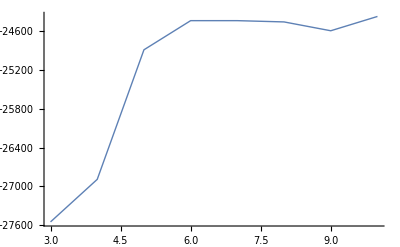

```mathematica
h2 = ListLinePlot[V1,PlotStyle->Thin,PlotRange->Full]
```

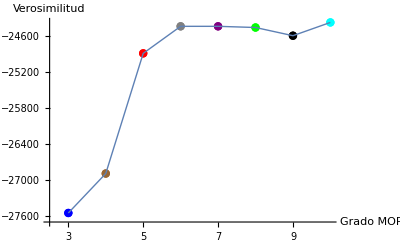

```mathematica
GrafVChiMuestra1=Show[h1,h2]
```

```mathematica
(*Gráfico verosimilitudes con otra muestra*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
data2 = RandomVariate[ChiSquareDistribution[5],10^4]
```

{3.92611,2.34812,4.86475,5.40946,9.92656,2.7506,5.57054,2.11573,2.97587,3.94655,2.96345,3.44625,6.41102,5.97522,1.41236,9970,5.86054,2.81497,2.71407,1.63191,1.32977,2.69402,3.82371,2.31427,4.14147,5.97406,3.2106,6.68792,2.10678,2.86916,1.42768}
 |  |  |  |

```mathematica
y3 = Log[f3[data2]]
```

{-2.60032,-2.82146,-2.54136,-2.52465,-2.75238,-2.74583,-2.52186,-2.87325,-2.71012,-2.59857,-2.71198,-2.64833,-2.52183,-2.5189,9972,-2.73518,-2.75204,-3.00539,-3.10941,-2.7555,-2.60943,-2.8286,-2.58301,-2.5189,-2.67728,-2.52682,-2.87538,-2.7265,-3.07353}
 |  |  |  |

```mathematica
y4=Log[f4[data2]]
```

{-2.42917,-2.55678,-2.44089,-2.46923,-3.17404,-2.50109,-2.48031,-2.5988,-2.47791,-2.42886,-2.47905,-2.44484,-2.55655,-2.51325,9972,-2.49393,-2.50535,-2.71627,-2.81675,-2.50776,-2.43115,-2.56241,-2.42726,-2.51315,-2.459,-2.58812,-2.60058,-2.48824,-2.7814}
 |  |  |  |

```mathematica
y5=Log[f5[data2]]
```

{-2.06167,-2.11188,-2.14711,-2.22522,-3.54338,-2.0682,-2.25196,-2.15072,-2.05454,-2.06279,-2.05512,-2.04635,-2.41692,-2.32614,9972,-2.06358,-2.07109,-2.2749,-2.39407,-2.07276,-2.05661,-2.11685,-2.07523,-2.32591,-2.04728,-2.48034,-2.15245,-2.06014,-2.35096}
 |  |  |  |

```mathematica
y6=Log[f6[data2]]
```

{-1.99878,-2.00009,-2.11314,-2.20682,-3.52746,-1.96833,-2.2379,-2.03249,-1.96161,-2.00054,-1.9618,-1.96823,-2.42286,-2.32232,9972,-1.96568,-1.97011,-2.14513,-2.25942,-1.97117,-1.99048,-2.0041,-2.01912,-2.32207,-1.9617,-2.49166,-2.03399,-1.96391,-2.2176}
 |  |  |  |

```mathematica
y7=Log[f7[data2]]
```

{-2.02759,-2.03525,-2.13882,-2.23106,-3.52838,-2.00189,-2.26176,-2.06849,-1.99423,-2.02928,-1.99447,-1.99891,-2.44506,-2.34533,9972,-1.99897,-2.00381,-2.18234,-2.29663,-2.00496,-2.01968,-2.03938,-2.04715,-2.34508,-1.99335,-2.51337,-2.07001,-1.99698,-2.25491}
 |  |  |  |

```mathematica
y8=Log[f8[data2]]
```

{-1.97854,-2.00232,-2.09786,-2.19933,-3.54388,-1.9607,-2.23327,-2.04182,-1.94975,-1.98028,-1.95015,-1.95038,-2.43604,-2.32578,9972,-1.95674,-1.96325,-2.17264,-2.30066,-1.96474,-1.97045,-2.00729,-1.99895,-2.3255,-1.94639,-2.51128,-2.0436,-1.95394,-2.2542}
 |  |  |  |

```mathematica
y9=Log[f9[data2]]
```

{-1.99733,-2.01805,-2.13103,-2.24067,-3.45816,-1.97285,-2.27666,-2.0615,-1.96147,-1.99934,-1.96186,-1.96409,-2.48482,-2.37306,9972,-1.96867,-1.97557,-2.20582,-2.34628,-1.97717,-1.98795,-2.02351,-2.02071,-2.37277,-1.95865,-2.55913,-2.06347,-1.96574,-2.29543}
 |  |  |  |

```mathematica
y10=Log[f10[data2]]
```

{-1.94921,-1.95391,-2.09739,-2.21232,-3.45138,-1.90915,-2.24921,-1.9993,-1.89955,-1.95156,-1.89983,-1.90818,-2.45663,-2.34639,9972,-1.90539,-1.91167,-2.15527,-2.31057,-1.91318,-1.93811,-1.95954,-1.97621,-2.3461,-1.89943,-2.52886,-2.00139,-1.90286,-2.25409}
 |  |  |  |

```mathematica
L3 = Apply[Plus,y3]
```

-27609.5

```mathematica
L4= Apply[Plus,y4]
```

-26896.6

```mathematica
L5= Apply[Plus,y5]
```

-24855.8

```mathematica
L6= Apply[Plus,y6]
```

-24396.1

```mathematica
L7= Apply[Plus,y7]
```

-24546.9

```mathematica
L8= Apply[Plus,y8]
```

-24412.7

```mathematica
L9= Apply[Plus,y9]
```

-24550.2

```mathematica
L10= Apply[Plus,y10]
```

-24342.6

```mathematica
L = {{{3,-27609.50103713608}},{{4,-26896.594385105156}},{{5,-24855.754886444356}},{{6,-24396.060931119475}},{{7,-24546.892065301196}},{{8,-24412.708964598474}},{{9,-24550.215007855935}},{{10,-24342.558002369893}}}
```

{{{3,-27609.5}},{{4,-26896.6}},{{5,-24855.8}},{{6,-24396.1}},{{7,-24546.9}},{{8,-24412.7}},{{9,-24550.2}},{{10,-24342.6}}}

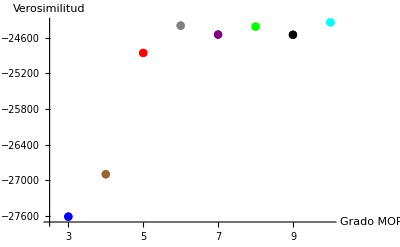

```mathematica
l1=ListPlot[L,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-27700},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,4,5,6,7,8,9,10}, Automatic}]
```

```mathematica
L1= {{3,-27609.50103713608},{4,-26896.594385105156},{5,-24855.754886444356},{6,-24396.060931119475},{7,-24546.892065301196},{8,-24412.708964598474},{9,-24550.215007855935},{10,-24342.558002369893}}
```

{{3,-27609.5},{4,-26896.6},{5,-24855.8},{6,-24396.1},{7,-24546.9},{8,-24412.7},{9,-24550.2},{10,-24342.6}}

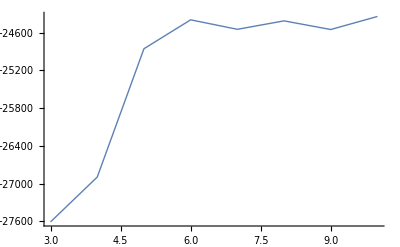

```mathematica
l2= ListLinePlot[L1,PlotStyle->Thin,PlotRange->Full]
```

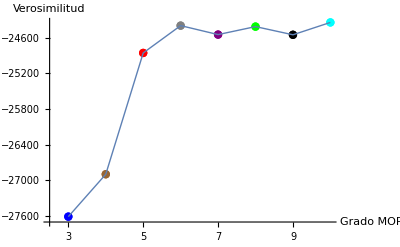

```mathematica
GrafVChiMuestra2=Show[l1,l2]
```

```mathematica
(*Comparación verosimilitudes con ambas muestras*)
```

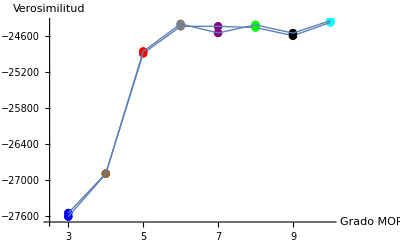

```mathematica
Show[GrafVChiMuestra1,GrafVChiMuestra2]
```